# TME2 M2 : Utilisation de Mathematica

## 1. Calculs formels

### A. Fonctions essentielles

```mathematica
1. == 1(* Rien a faire *)
```

True

```mathematica
1/(1/3+1/2)== 1/(5/6) == 6/5(* reduction au meme denominateur *)
```

True

```mathematica
5/7-2/7(1-3/4)== 5/7 - 2/7*(1/4) == 5/7 - 2/28 == 18/28 == 9/14(* reduction au meme denominateur et simplification *)
```

True

```mathematica
(* Mathematica compare chaque egalite a la valeur 9/14 pour retourner True ou False *)
```

```mathematica
N[-7-4 √2-2 √(2 (10+7 √2)), 5] * N[-7-4 √2+2 √(2 (10+7 √2)), 5] (* Multiplication proche de 1 *)
```

1.

```mathematica
-7-4 √2-2 √(2 (10+7 √2))* -7-4 √2+2 √(2 (10+7 √2)) == -7-8 √2+16 √(2 (10+7 √2))
```

True

```mathematica
Sin[x]^2+Cos[x]^2
```

```mathematica
Cos[x]^2+Sin[x]^2 (* Pas de simplification effectuer car mathematica utilise que les regles arithmetique par defaut *)
```

```mathematica
Simplify[Sin[x]^2+Cos[x]^2] (* Utilisation des regles de trigonometrie *)
```

1

```mathematica
Simplify[Sin[x]^2+Cos[x]^2==1]
```

True

```mathematica
Simplify[Abs[Cos[x]]==Cos[x]]
```

```mathematica
Abs[Cos[x]]==Cos[x] (* Pas de simplification car la condition est impossible *)
```

```mathematica
Simplify[Abs[Cos[x]]==Cos[x], x>0]
```

```mathematica
Abs[Cos[x]]==Cos[x] (* Pas de simplification car la condition est impossible *)
```

```mathematica
Simplify[Abs[Cos[x]]==Cos[x], x<0]
```

```mathematica
Abs[Cos[x]]==Cos[x] (* Pas de simplification car la condition est impossible *)
```

```mathematica
Simplify[Abs[Cos[x]]==Cos[x], 0<x<π]
```

```mathematica
Abs[Cos[x]]==Cos[x] (* Pas de simplification car la condition est impossible *)
```

```mathematica
Simplify[Abs[Cos[x]]==Cos[x], 0<x<π/2]
```

```mathematica
True (* Condition possible donc affichage de True *)
```

```mathematica
Simplify[Abs[Cos[x]]==Cos[x], -π/2<x<π/2]
```

```mathematica
True (* Condition possible donc affichage de True *)
```

```mathematica
Simplify[Abs[Cos[x]]==Cos[x], -π/2<x<π/2 && (-π/2+2π<x<π/2+2π)] (* Mathematica nous previent qu'il y a une contradiction dans notre equation mais il nous affiche quand meme le resultat en corrigeant notre erreur *)
```

Simplify::cas: Warning: contradictory assumption(s) -π/2<x<π/2&&(3 π)/2<x<(5 π)/2 encountered.

```mathematica
True
```

```mathematica
(* La condition la plus simple est celle faisant intervenir 0<x<π/2 car elle decrit bien la partie positive du debut de cos(x) *)
```

```mathematica
Simplify[Sqrt[x^2]] (* Pas de simplification car nous sommes dans le monde des complexes de base *)
```

√(x^2)

```mathematica
Simplify[Sqrt[x^2],x≥0] (* simplification possible maintenant dans R *)
```

x

```mathematica
PowerExpand[Sqrt[x^2]] (* fonctionne car PowerExpand suppose que x est positif comme au dessus *)
```

x

```mathematica
Simplify[Sqrt[x^2],Element[x,Reals]]==Simplify[√(x^2),x∈Reals]==Abs[x] (* On peut specifier que x appartient au reel pour pouvoir faire la simplification *)
```

True

```mathematica
Simplify[Sin[x+2*n*Pi]==Sin[x] ,Element[n,Integers]]
```

True

```mathematica
Simplify[Cos[n*Pi/2-x]==?????, Element[(n-1)/4,Integers]](* Pas trouve *)
```

```mathematica
Simplify[Log[x^r]]
```

Log[x^r]

```mathematica
Simplify[Log[x^r],x>0]
```

Log[x^r]

```mathematica
Simplify[Log[x^r],Element[r,Reals]]
```

Log[x^r]

```mathematica
Simplify[Log[x^r],x>0&&Element[r,Reals]] (* Il faut bien que tout les conditions soient reunits pour pouvoir faire la simplification *)
```

r Log[x]

```mathematica
Simplify[5 Log2[a^2]− 2 Log2[a], a >0 ] (* On simplifie et specifie bien que a doit etre superieur a 0 *)
```

(8 Log[a])/Log[2]

### B. Fonction pure

```mathematica
5*#+6&[2] (* Les fonctions pure sont des fonctions qui n'ont pas de nom. C'est utile car on peut faire des calculs plus rapidemment vu qu'on a pas besoin de rechercher la fonction donnée dans la mémoire *)
```

16

## 2. Listes

### A. Définition et Opérations immédiates

```mathematica
liste1={3,9,14,13,87,4,2}
```

{3,9,14,13,87,4,2}

```mathematica
liste1[[7]]
```

77

```mathematica
liste1+2
```

{5,7,13,15,27,38,79}

```mathematica
-1+liste1
```

{2,4,10,12,24,35,76}

```mathematica
(-1+liste1) Simplify
```

{2 Simplify,4 Simplify,10 Simplify,12 Simplify,24 Simplify,35 Simplify,76 Simplify}

```mathematica
liste1 *10
```

{30,50,110,130,250,360,770}

```mathematica
liste1/5
```

{3/5,1,11/5,13/5,5,36/5,77/5}

```mathematica
liste1*liste1
```

{9,25,121,169,625,1296,5929}

```mathematica
liste1^2
```

{9,25,121,169,625,1296,5929}

```mathematica
(liste1)^2
```

{9,25,121,169,625,1296,5929}

```mathematica
N[ArcSin[liste1]] (* On peut effectuer les d'opérations sur tout l'ensemble au lieu de le faire element par element en utilisannt les listes ! *)
```

{1.24905,1.3734,1.48014,1.49402,1.53082,1.54303,1.55781}

```mathematica
liste2={1,2,3,4,5, 6, 7}
```

{1,2,3,4,5,6,7}

```mathematica
liste1+liste2
```

{4,11,17,17,92,10,9}

```mathematica
liste1-(3*liste2)
```

{0,3,5,1,72,-14,-19}

{-19,-14,0,1,3,5,72}

```mathematica
liste2/liste1 (* Les opérations sont possibles entre 2 listes si elles sont de même taille.
```

```mathematica
liste2bis={1, 2, 3, 4}
```

{1,2,3,4}

```mathematica
liste2bis + liste2 (* Erreur car pas de même taille *)
```

Thread::tdlen: Objects of unequal length in {1,2,3,4}+{1,2,3,4,5,6,7} cannot be combined.

{1,2,3,4}+{1,2,3,4,5,6,7}

```mathematica
liste4={1,2,3,{4,4},5,6,7}
```

{1,2,3,{4,4},5,6,7}

```mathematica
liste2 + liste4 (* le tuple 4,4 est considéré comme un seul élément et il est donc additionné à l'élément au même index de la liste 2. *)
```

{2,4,6,{8,8},10,12,14}

### B. Générations de listes

```mathematica
Table[i*7,{i,14}]
```

{7,14,21,28,35,42,49,56,63,70,77,84,91,98}

```mathematica
Range[7,100,7]
```

{7,14,21,28,35,42,49,56,63,70,77,84,91,98}

```mathematica
liste5={7,14,21,28,35,42,49,56,63,70,77,84,91,98}
```

{7,14,21,28,35,42,49,56,63,70,77,84,91,98}

```mathematica
Table[i*7,{i,1000/7}]//Timing
```

{0.,{7,14,21,28,35,42,49,56,63,70,77,84,91,98,105,112,119,126,133,140,147,154,161,168,175,182,189,196,203,210,217,224,231,238,245,252,259,266,273,280,287,294,301,308,315,322,329,336,343,350,357,364,371,378,385,392,399,406,413,420,427,434,441,448,455,462,469,476,483,490,497,504,511,518,525,532,539,546,553,560,567,574,581,588,595,602,609,616,623,630,637,644,651,658,665,672,679,686,693,700,707,714,721,728,735,742,749,756,763,770,777,784,791,798,805,812,819,826,833,840,847,854,861,868,875,882,889,896,903,910,917,924,931,938,945,952,959,966,973,980,987,994}}

```mathematica
Range[7,1000,7]//Timing (* La fonction range est plus rapide que la fonction Table, mais la fonction Table permet plus de chose que la fonction range. *)
```

{0.,{7,14,21,28,35,42,49,56,63,70,77,84,91,98,105,112,119,126,133,140,147,154,161,168,175,182,189,196,203,210,217,224,231,238,245,252,259,266,273,280,287,294,301,308,315,322,329,336,343,350,357,364,371,378,385,392,399,406,413,420,427,434,441,448,455,462,469,476,483,490,497,504,511,518,525,532,539,546,553,560,567,574,581,588,595,602,609,616,623,630,637,644,651,658,665,672,679,686,693,700,707,714,721,728,735,742,749,756,763,770,777,784,791,798,805,812,819,826,833,840,847,854,861,868,875,882,889,896,903,910,917,924,931,938,945,952,959,966,973,980,987,994}}

```mathematica
liste0=RandomInteger[{1, 1000}, 100]
```

{569,971,902,846,274,458,350,319,612,663,245,532,185,762,335,865,234,84,516,903,578,335,595,509,124,726,270,54,419,62,238,280,65,967,288,975,605,267,347,688,611,578,626,958,321,987,885,418,386,230,530,143,525,665,474,412,404,550,170,798,150,875,765,660,871,379,246,585,509,291,453,809,434,933,632,969,807,368,147,713,414,646,859,412,811,893,942,561,998,330,935,507,416,575,189,147,80,497,177,900}

```mathematica
Select[liste0, ((Mod[#-1, 4]==0)|| (MOd[#+1, 4]==0))&]
```

{569,245,185,865,509,65,605,321,885,525,665,765,585,509,453,809,933,969,713,893,561,189,497,177}

```mathematica
Select[liste0, PrimeQ]
```

{569,971,509,419,967,347,379,509,809,859,811}

```mathematica
Timing[Range[10^3];]
```

{0.,Null}

```mathematica
Timing[Table[i,{10^3}];]
```

{0.,Null}

```mathematica
Timing[listeDo ={};
Do[listeDo=Append[listeDo,i],{i,1,10^3}];] (* Je ne comprends pas pourquoi je n'ai pas de résultats... *)
```

{0.,Null}

```mathematica
Apply[Plus,Range[10^6]]//Timing
Total[Range[10^6]]//Timing
Apply[Plus,Table[i,{i,1,10^6}]]//Timing
Do  (s=0;Do[s=s+i,{i,1,10^6}];s)//Timing
Sum[i,{i,1,10^6}]//Timing
NSum[i,{i,1,10^6}]//Timing
(Sum[i,{i,1,n}]/.n->10^6)//Timing
Manipulate[Sum[i^k,{i,1,n}],{{k,1},1,50,1}] (* La méthode la plus rapide est la dernière *)
```

{0.109375,500000500000}

{0.,500000500000}

{0.125,500000500000}

{0.359375,500000500000 Do}

{0.09375,500000500000}

{0.,5.00001×10^11}

{0.,500000500000}

```mathematica
{0.,500000500000
```

### C. Opérations sur les listes

```mathematica
Map[Length, {liste3, liste4, liste0}] (* Map applique la fonction length a toute les listes en argument *)
```

{7,7,100}

```mathematica
Total[liste0] (* Total calcule la somme des élements de la liste *)
```

52573

```mathematica
Map[Total, {liste3, liste4,liste5, liste0}]
```

{170,{28,28},735,52573}

### D. Mise en forme et Représentations de listes

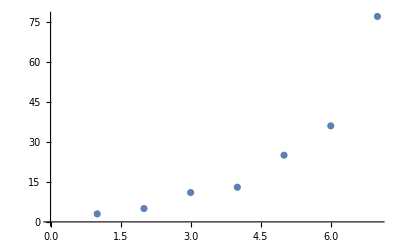

```mathematica
ListPlot[liste3]
```

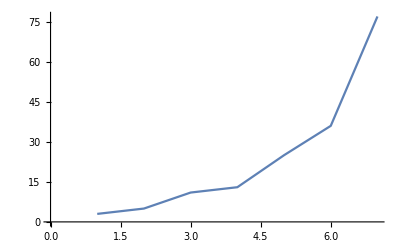

```mathematica
ListPlot[liste3, Joined-> True]
```

```mathematica
ListLinePlot[liste3]==ListPlot[liste3,Joined->True]
```

-Graphics-==-Graphics-

```mathematica
listePLot=Table[{x, 2x}, {x, 2,12, 2}]
```

{{2,4},{4,8},{6,12},{8,16},{10,20},{12,24}}

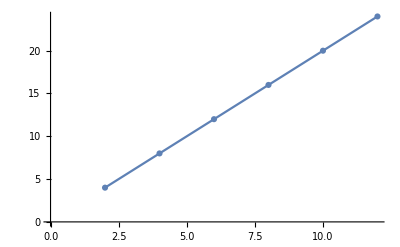

```mathematica
ListPlot[listePLot, Joined-> True,PlotMarkers-> Automatic]
```

```mathematica
liste8=Table[
Cos[i+k(π/30)]Cos[j],
{i,0,2π,0.6},{j,0,2π,0.6},{k,0,30,1}
];
```

```mathematica
ListAnimate[ (* Il y a une alternance de deux phases qui varie suivant les differentes valeurs de i,j,k. *)
Map[
ListContourPlot,
liste8
]
]
```

```mathematica
liste7=Table[{i,i^2},{i, 3.1,8.5,0.5}]
```

{{3.1,9.61},{3.6,12.96},{4.1,16.81},{4.6,21.16},{5.1,26.01},{5.6,31.36},{6.1,37.21},{6.6,43.56},{7.1,50.41},{7.6,57.76},{8.1,65.61}}

```mathematica
liste7MiseEnForme=TableForm[liste7]
```

3.1 | 9.61
3.6 | 12.96
4.1 | 16.81
4.6 | 21.16
5.1 | 26.01
5.6 | 31.36
6.1 | 37.21
6.6 | 43.56
7.1 | 50.41
7.6 | 57.76
8.1 | 65.61

```mathematica
liste7*3
```

{{9.3,28.83},{10.8,38.88},{12.3,50.43},{13.8,63.48},{15.3,78.03},{16.8,94.08},{18.3,111.63},{19.8,130.68},{21.3,151.23},{22.8,173.28},{24.3,196.83}}

```mathematica
liste7MiseEnForme*3 (* Ne fonctionne pas avec TableForm car c'est un object permettant seulement l'affichage et non les opérations *)
```

3 3.1 | 9.61
3.6 | 12.96
4.1 | 16.81
4.6 | 21.16
5.1 | 26.01
5.6 | 31.36
6.1 | 37.21
6.6 | 43.56
7.1 | 50.41
7.6 | 57.76
8.1 | 65.61

## 3. Programmation fonctionnelle et Programmation par règles

```mathematica
(x+3y)/.{x->y,y->z} (* On peut faire de la substitution de variable dans les fonctions *)
```

y+3 z

```mathematica
(x+3y)/.{x->y}/.{y->z} (* Ici on a deux substitutions de suite, c'est pourquoi on se retrouve qu'avec des z *)
```

4 z

```mathematica
list9={A,C,G,T,G,T,A,C,G,T,G,T}
```

{A,C,G,T,G,T,A,C,G,T,G,T}

```mathematica
(list9)/. {A -> T,C-> G, G->C, T->A} (* On utilise la substitution pour faire le complémentaire de la séquence *)
```

{T,G,C,A,C,A,T,G,C,A,C,A}

## 4. Traitement d’expressions symboliques

### A. Transformations algébriques

```mathematica
m=Expand[-1/2((1-√a)^8-(1+√a)^8)((1-√a)^8+(1+√a)^8)√a] (* Developpement d'une equation *)
```

16 a+560 a^2+4368 a^3+11440 a^4+11440 a^5+4368 a^6+560 a^7+16 a^8

```mathematica
Factor[x^2-3] (* Pas de factorisation possible *)
```

-3+x^2

```mathematica
f[x]=((x+3)(x-1)^2)/((x^2+1)(x+5)^2)
```

((-1+x)^2 (3+x))/((5+x)^2 (1+x^2))

```mathematica
Expand[f[x]] (* Developpement de la fonction f *)
```

3/((5+x)^2 (1+x^2))-(5 x)/((5+x)^2 (1+x^2))+x^2/((5+x)^2 (1+x^2))+x^3/((5+x)^2 (1+x^2))

```mathematica
ExpandAll[f[x]] (* Developpement maxixum possible donc plus aucune parenthèse *)
```

3/(25+10 x+26 x^2+10 x^3+x^4)-(5 x)/(25+10 x+26 x^2+10 x^3+x^4)+x^2/(25+10 x+26 x^2+10 x^3+x^4)+x^3/(25+10 x+26 x^2+10 x^3+x^4)

```mathematica
ExpandDenominator[f[x]] (* Developpe seulement le denominateur *)
```

((-1+x)^2 (3+x))/(25+10 x+26 x^2+10 x^3+x^4)

```mathematica
ExpandNumerator[f[x]] (* Developpe seulement le numerateur *)
```

(3-5 x+x^2+x^3)/((5+x)^2 (1+x^2))

```mathematica
ExpandDenominator[Together[1/(x^2-16)-(x+4)/(x^2-3 x-4)]] (* Developpe seulement le denominateur, Together est utilisé pour mettre sous le même denominateur *)
```

(-15-7 x-x^2)/(-16-16 x+x^2+x^3)

### C. Transformer des expressions trigonométriques

```mathematica
f [y_]:=Sin[y]^2+Tan[y]^2 (* TrigExpand developpe l'expression en utilisant les regles de trigonometres, TrigReduce simplifie et reduit l'expression, TriFactor factorise. *)
TrigExpand[f[y]]
TrigReduce[f[y]]
TrigFactor[f[y]]
```

-1/2-Cos[y]^2/8+(5 Sec[y]^2)/8+(3 Sin[y]^2)/4+Tan[y]^2/2-1/8 Sin[y]^2 Tan[y]^2

1/8 (5 Sec[y]^2-4 Cos[2 y] Sec[y]^2-Cos[4 y] Sec[y]^2)

1/2 (3+Cos[2 y]) Tan[y]^2

```mathematica
Sin[a+b]==Simplify[Sin[a]*Cos[b]+Cos[a]*Sin[b]]
```

True

```mathematica
Simplify[(1-Cot[a])^2+(1-Tan[a])^2==(Sec[a]-Csc[a])^2]
```

True